```mathematica
pos[θ_,ϕ_]:={Sin[ϕ] Sin[θ],Cos[ϕ]Sin[θ],Cos[θ]}
```

```mathematica
PlotList[lis_,liscoord_]:=Table[
Graphics[
{Blend[{White,Black},.5(1+lis[[i,1]])],PointSize[0.04],Point[{liscoord[[i,2]],liscoord[[i,1]]}]
}
],
{i,Length@lis}]//Show[#,AspectRatio->1]&
PlotList1[lis_,liscoord_]:=Table[
Graphics3D[
{Blend[{White,Black},.5(1+lis[[i,1]])],PointSize[0.04],Point[{Sin[liscoord[[i,1]]]Cos[liscoord[[i,2]]],Sin[liscoord[[i,1]]]Sin[liscoord[[i,2]]],Cos[liscoord[[i,1]]]}]
}
],
{i,Length@lis}]//Show[#,AspectRatio->1]&
PlotList2[lis_,liscoord_]:=Table[
Δθ=2Min@liscoord[[;;,1]];
Δϕ=Min@liscoord[[;;,2]];
Graphics3D[
{Glow[Blend[{White,Black},.5(lis[[i,1]]+1)]],
EdgeForm[Transparent],
Polygon[
{pos[liscoord[[i,1]]+Δθ/2,liscoord[[i,2]]+Δϕ/2],
pos[liscoord[[i,1]]+Δθ/2,liscoord[[i,2]]-Δϕ/2],
pos[liscoord[[i,1]]-Δθ/2,liscoord[[i,2]]-Δϕ/2],
pos[liscoord[[i,1]]-Δθ/2,liscoord[[i,2]]+Δϕ/2]}
]}
],
{i,Length@lis}]//Show[#,Boxed->False,Lighting->None]&
```

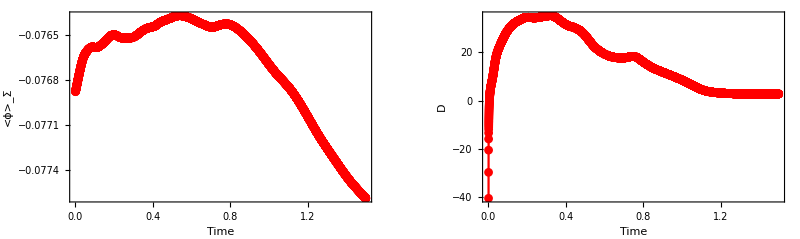

```mathematica
nofFiles=Length@FileNames["s-t*.dat",NotebookDirectory[]][[;;]];δplots=Round[(nofFiles-1)/15];
hiList=Import[ToString[NotebookDirectory[]]<>"hi.dat"];
coordList=Import[ToString[NotebookDirectory[]]<>"coord.dat"];
GraphicsRow[{ListPlot[hiList[[;;,{1,2}]],Frame->True,Axes->False,FrameStyle->Large,ImageSize->1000,Joined->True,PlotStyle->Red,PlotMarkers->{"•", 9},FrameLabel-> {"Time","<ϕ>_Σ"}],
ListPlot[hiList[[;;,{1,3}]],Frame->True,Axes->False,FrameStyle->Large,ImageSize->1000,Joined->True,PlotStyle->Red,PlotMarkers->{"•", 9},FrameLabel-> {"Time","D"}]},ImageSize->Full]
```

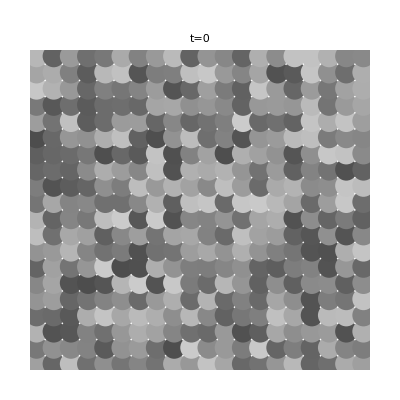
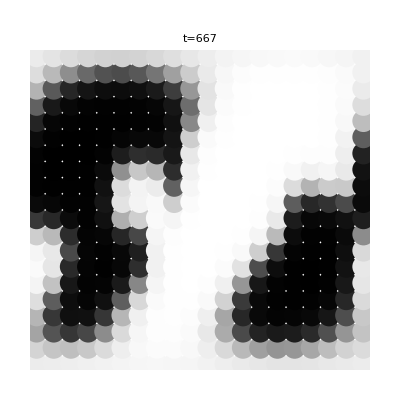
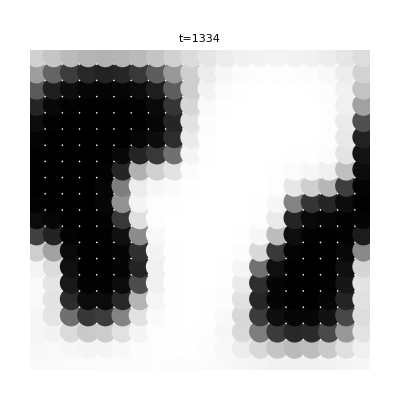
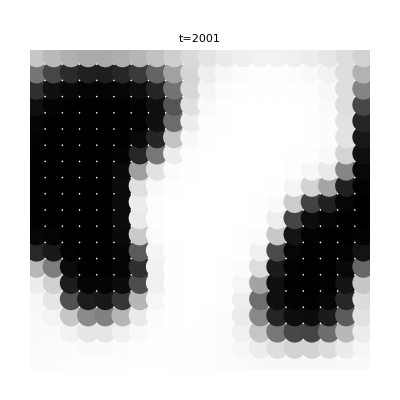
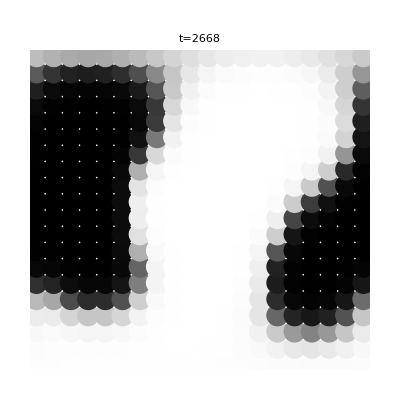
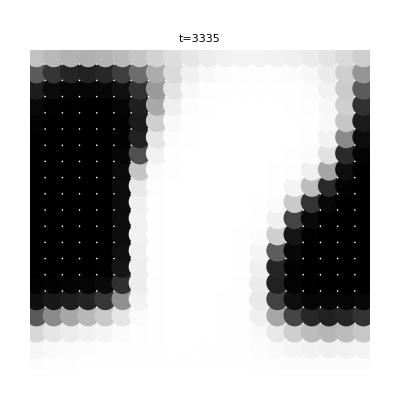
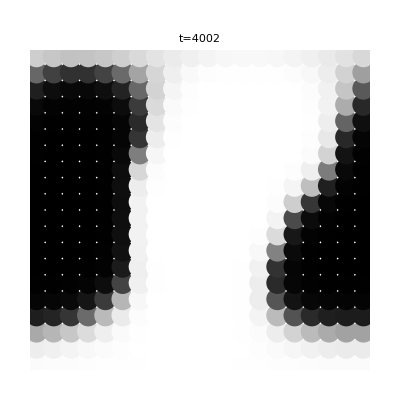
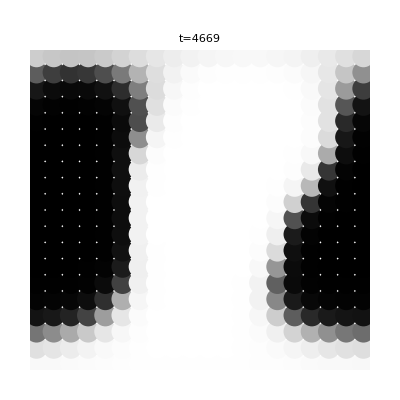

```mathematica
Table[Show[PlotList[Import[ToString[NotebookDirectory[]]<>"s-t"<>ToString[i]<>".dat"],coordList],PlotLabel->"t="<>ToString[i]],{i,0,nofFiles,δplots}]
```

```mathematica
(*Table[PlotList1[Import[ToString[NotebookDirectory[]]<>"s-t"<>ToString[i]<>".dat"]],{i,0,nofFiles,δplots}]*)
```

```mathematica
(*Table[Show[PlotList2[Import[ToString[NotebookDirectory[]]<>"s-t"<>ToString[i]<>".dat"],coordList],PlotLabel->"t="<>ToString[i]],{i,0,nofFiles,δplots}]*)
```

```mathematica
numframes=400;
listaMovie=Table[Show[PlotList2[Import[ToString[NotebookDirectory[]]<>"s-t"<>ToString[i]<>".dat"],coordList],PlotLabel->"t="<>ToString[i],ImageSize->800,ViewPoint->2{Cos[2π i/nofFiles]Cos[π/6],Sin[π/6]Cos[2π i/nofFiles],  Sin[2π i/nofFiles]}],{i,0,nofFiles,Round[(nofFiles-1)/numframes]}];
```

Import::nffil: File not found during Import.

Show::shx: No graphical objects to show.

Show::gtype: Show is not a type of graphics.

```mathematica
Export[ToString[NotebookDirectory[]]<>"video1.avi",listaMovie]
```

/home/pier/Desktop/GitRepos/Sphere/sphere2dp/video1.avi